Thomas Kwok
Math 385

# Homework 2

## Problem 1

Plot the function f(x) = xe^(-^x) - 0.16064.

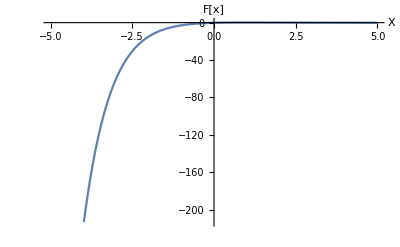

```mathematica
F[x_]:= x*(ⅇ^-x) - .16064
Plot[F[x], {x, -5, 5}, AxesLabel -> {"X", "F[x]"}]
```

a. Use FindRoot to locate a root near x =3

```mathematica
F[x_]:= x*(ⅇ^-x) - .16064
FindRoot[F[x], {x, 3}]
```

{x→2.88976}

b. Use a program in Mathematica implementing Newton’s Method. Use your program to approximate the root near x = 3. Set the maximal number of iterations to 100 and the kick out threshold to 10^-5. Display a table. How many iterations before it stops?

```mathematica
F[x_]:= x*(ⅇ^-x) - 0.16064
Seed = 3;
Seed2 = 0;
i = 1;
iter = 100;
l = {};
While[Abs[Seed-Seed2] ≥  10^(-5) && i < iter,
AppendTo[l, {i, N[Seed], N[F[Seed]], Abs[Seed-Seed2]}];
Seed2 = Seed;
Seed = Seed - F[Seed]/F'[Seed];
i++;]
dtable = Table[l[[i]], {i, i-1}];
dheader = PrependTo[dtable, {"iteration", "approximate root", "residue", "|Xn-Xn-1|"}];
Grid[dheader, Dividers-> All]
```

iteration | approximate root | residue | |Xn-Xn-1|
1 | 3. | -0.0112788 | 3
2 | 2.88673 | 0.000319031 | 0.11327
3 | 2.88976 | 2.27381×10^-7 | 0.00303259

C. Redo (b) with a kick out threshold set to 10^-2. Find the Relative Absolute Error.

```mathematica
F[x_]:= x*(ⅇ^-x) - .16064
root = x /.FindRoot[F[x], {x, 3}];
Seed = 3;
Seed2 = 0;
i = 1;
iter = 100;
l = {};
While[Abs[Seed-Seed2] > 10^(-2) && i < iter,
AppendTo[l, {i, N[Seed], N[F[Seed]], Abs[Seed-Seed2], Abs[(F[root]-F[Seed])/F[root]]}];
Seed2 = Seed;
Seed = Seed - F[Seed]/F'[Seed];
i++;]
dtable = Table[l[[i]], {i, i-1}];
dheader = PrependTo[dtable, {"iteration", "approximate root", "residue", "|Xn-Xn-1|", "Absolute Relative Error"}];
Grid[dheader, Dividers-> All]
```

iteration | approximate root | residue | |Xn-Xn-1| | Absolute Relative Error
1 | 3. | -0.0112788 | 3 | 4.06361×10^14
2 | 2.88673 | 0.000319031 | 0.11327 | 1.14943×10^13

## Problem 2

f(x) = x/(x^2+1) with points (1.5, f(1.5))

a. Use FindRoot to solve f(x) = 0 starting at 1.5. What happens? Why?

The function failed to converge to the requested accuracy within 100 iterations. This is because x=1.5 was a very small number to choose for our first guess of the root.

```mathematica
F[x_]:= x/(x^2+1)
FindRoot[F[x], {x, 1.5}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→3.58215×10^30}

b. Write your own Newton execution starting at 1.5, what is the first ten iterations?

```mathematica
F[x_]:=  x/(x^2+1)
Seed = 1.5;
Seed2 = 0;
i = 1;
iter = 10;
l = {};
While[Abs[Seed-Seed2] > 10^(-5) && i ≤ iter,
AppendTo[l, {i, N[Seed], N[F[Seed]], Abs[Seed-Seed2]}];
Seed2 = Seed;
Seed = Seed - F[Seed]/F'[Seed];
i++;]
dtable = Table[l[[i]], {i, i-1}];
dheader = PrependTo[dtable, {"iteration", "approximate root", "residue", "|Xn-Xn-1|"}];
Grid[dheader, Dividers-> All]
```

iteration | approximate root | residue | |Xn-Xn-1|
1 | 1.5 | 0.461538 | 1.5
2 | 5.4 | 0.179045 | 3.9
3 | 11.1835 | 0.088708 | 5.78352
4 | 22.5473 | 0.0442641 | 11.3638
5 | 45.1835 | 0.0221211 | 22.6362
6 | 90.4113 | 0.0110592 | 45.2278
7 | 180.845 | 0.00552943 | 90.4334
8 | 361.701 | 0.0027647 | 180.856
9 | 723.407 | 0.00138235 | 361.706
10 | 1446.82 | 0.000691172 | 723.41

c. Plot f along with the tangent line on the 4th iteration. Put both plots on same axis. How does the tangent line help explain part b?

The tangent line is a visual representation of what we are doing in part B. The Newton method creates a tangent line using our seed to find the value closest to the root and the tangent line shows it. Both show that it is close to the root but only to 10^-2 so there can still be much more iterations.

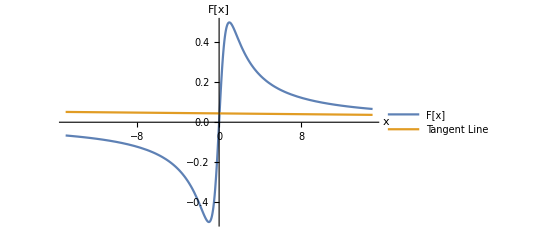

```mathematica
F[x_]:=  x/(x^2+1)
i = 0;
Seed = 1.5;
While[Abs[Seed-Seed2] > 10^(-5) && i < 4,
Seed2 = Seed;
Seed = Seed - F[Seed]/F'[Seed];
i++;]
a = Seed;
G[x_] := F'[a]*(x-a)+F[a]
Plot[{F[x], G[x]}, {x, -15, 15}, AxesLabel-> {"x", "F[x]"}, PlotLegends-> {"F[x]", "Tangent Line"}]
```

## Problem 3

Consider the function f(x) = (x-1)^2 -2 which has a root at 1+√2

a. Use FindRoot to estimate the root of f(x) with seeds at 2 and 3. Note this will default to the Secant Method

```mathematica
F[x_]:= (x-1)^2 -2;
FindRoot[F[x], {x, 2, 3}]
```

{x→2.41421}

b. Repeat the exercise with Newton’s method with initial seed 3

```mathematica
F[x_]:=  (x-1)^2 -2;
Seed = 3;
Seed2 = 0;
i = 0;
iter = 100;
l = {};
While[Abs[Seed-Seed2] > 10^(-5) && i ≤ iter,
AppendTo[l, {i, N[Seed], N[F[Seed]], Abs[Seed-Seed2]}];
Seed2 = Seed;
Seed = Seed - F[Seed]/F'[Seed];
i++;]
dtable = Table[l[[i]], {i, i}];
dheader = PrependTo[dtable, {"iteration", "approximate root", "residue", "|Xn-Xn-1|"}];
Grid[dheader, Dividers-> All]
```

iteration | approximate root | residue | |Xn-Xn-1|
0 | 3. | 2. | 3
1 | 2.5 | 0.25 | 1/2
2 | 2.41667 | 0.00694444 | 1/12
3 | 2.41422 | 6.0073×10^-6 | 1/408

c. Estimate the absolute error using roots from Newton’s method and Secant method.

```mathematica
F[x_]:=  (x-1)^2 -2;
Seed = 3;
Seed2 = 0;
i = 0;
iter = 100;
l = {};
While[Abs[Seed-Seed2] > 10^(-5) && i ≤ iter,
Seed2 = Seed;
Seed = Seed - F[Seed]/F'[Seed];
i++;]
a = x /. FindRoot[F[x], {x, 2, 3}];
Print["Absolute Error -> ", Abs[F[Seed]-F[a]]]
```

Absolute Error -> 4.51139×10^-12

d. Use the true root to calculate the actual absolute error and show it is less than the estimated absolute error

```mathematica
F[x_]:=  (x-1)^2 -2;
Seed = 3;
Seed2 = 0;
i = 0;
iter = 100;
l = {};
While[Abs[Seed-Seed2] > 10^(-5) && i ≤ iter,
Seed2 = Seed;
Seed = Seed - F[Seed]/F'[Seed];
i++;]
a = x /. FindRoot[F[x], {x, 2, 3}];
c = 1+√2;
estimate= Abs[F[Seed]-F[a]];
actual = Abs[F[Seed] - F[c]];
Print["Difference between estimate and actual -> ", estimate-actual]
Print["Difference between actual and estimate -> ", actual - estimate]
```

Difference between estimate and actual -> 4.44089×10^-16

Difference between actual and estimate -> -4.44089×10^-16

## Problem 4

Consider the function f(x) = xe^(-^x) - 0.16064

a. Use FindRoot to locate a root between x=2 and x=3

```mathematica
F[x_]:= x*(ⅇ^-x) - .16064;
FindRoot[F[x], {x, 2, 3}]
```

{x→2.88976}

b. Write a program implementing the secant method. Set maximal number of iterations to 100 and the kick out threshold to 10^-5. Display the approximate root, residual, and |Xn-Xn-1| at each iteration in a table.

```mathematica
F[x_]:= x*(ⅇ^-x) - 0.16064
X0 = 3;
X1 = 2;
X2 = 0;
i = 1;
iter = 100;
l = {};
While[Abs[X0-X1] ≥  10^(-5) && i < iter && X0 ≠ X1 && F[X0] ≠ F[X1],
AppendTo[l, {N[X0], N[F[X0]], Abs[X0-X1]}];
X2 = X0;
X0 = X0 -(F[X0]*(X0-X1))/(F[X0]-F[X1]);
X1 = X2;
i++;]
dtable = Table[l[[i]], {i, i-1}];
dheader = PrependTo[dtable, {"approximate root", "residue", "|Xn-Xn-1|"}];
Grid[dheader, Dividers-> All]
```

approximate root | residue | |Xn-Xn-1|
3. | -0.0112788 | 1
2.90702 | -0.00180581 | 0.0929755
2.8893 | 0.000048707 | 0.0177237
2.88977 | -1.98808×10^-7 | 0.000465494

c. How many iterations does your program execute? Compare its speed of convergence to Problem 1

```mathematica
F[x_]:= x*(ⅇ^-x) - 0.16064
X1 = 3;
X0 = 2;
X2 = 0;
i = 1;
iter = 100;
l = {};
While[Abs[X1-X0] ≥  10^(-5) && i < iter,
AppendTo[l, {i}];
X2 = X1;
X1 = X1 -(F[X1]*(X1-X0))/(F[X1]-F[X0]);
X0 = X2;
i++;]
dtable = Table[l[[i]], {i, i-1}];
dheader = PrependTo[dtable, {"iteration"}];
Grid[dheader, Dividers-> All]
```

iteration
1
2
3
4

The program executed 4 iterations in order to get the Secant Root. This was one more iteration than my program in Problem 1 but the residue is closer to the root than the one in Problem 1. So although the speed of convergence of the Newton method surpasses the Secant method rate of convergence, the Secant method does a better job approaching the actual root.

d. Use ListPlot to display 5 Newton’s method estimates along with 5 secant method estimates. Use different symbols for the two plots. Comment on result.

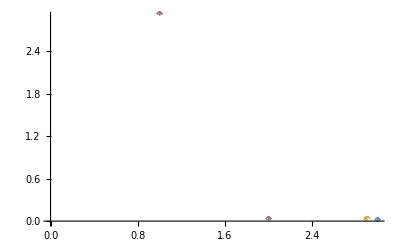

```mathematica
F[x_]:= x*(ⅇ^-x) - 0.16064
X0 = 3;
X1= 2;
X2 = 0;
Seed = 3;
Seed2 = 0;
i = 1;
l = {};
m = {};
n = {};
p = {};
iter = 100;
While[Abs[X0-X1] ≥  10^(-6)&& i < iter,
X2 = X0;
Seed2 = Seed;
AppendTo[n, N[X0]];
AppendTo[p, N[Seed]];
AppendTo[l, N[F[X0]]];
AppendTo[m, N[F[Seed]]];
Seed = Seed - F[Seed]/F'[Seed];
X0 = X0 -(F[X0]*(X0-X1))/(F[X0]-F[X1]);
X1 = X2;
i++;]
mysecantplot = ListPlot[{{{n[[1]], l[[1]]}}, {{n[[2]], l[[2]]}}, {n[[3]], l[[3]]}, {n[[4]], l[[4]]}, {n[[5]], l[[5]]}}, PlotMarkers -> "^", PlotLegends-> "^" Secant];
mynewtonplot = ListPlot[{{{p[[1]], m[[1]]}}, {{p[[2]], m[[2]]}}, {p[[3]], m[[3]]}, {p[[4]], m[[4]]}, {p[[5]], m[[5]]}}, PlotMarkers->"*", PlotLegends-> "*" Newton];
Show[mysecantplot, mynewtonplot]
```